# Lognormal Pathology

```mathematica
Limit[CDF[LogNormalDistribution[-1/2 σ^2,σ],ϵ],σ->∞]
```

Piecewise[{{1, ϵ>0}, {0, True}}]

```mathematica
?CDF[LogNormalDistribution[-1/2 σ^2,σ],ϵ]
```

Information[Piecewise[{{1/2 Erfc[(-σ^2/2-Log[ϵ])/(√2 σ)], ϵ>0}, {0, True}}],LongForm→False]

```mathematica
?CDF
```

## Lognormal at High Variance

```mathematica
?LogNormalDistribution
```

```mathematica
?Clear
```

You can see at low variance, the lognormal looks normal.
In reality, it is not.

```mathematica
Clear[σ];Clear[x];
```

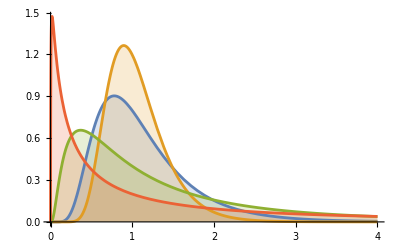

```mathematica
Plot[Table[PDF[LogNormalDistribution[1/1000,σ],x],{σ,{1/2,1/3,1,2}}]//Evaluate,{x,0,4},Filling->Axis]
```